```mathematica
Needs["NDSolve`FEM`"]
RoundedPolygon=ResourceFunction["RoundedPolygon"];
```

```mathematica
v1 = {{0, 0, -.1}, {0, 0, 1.1}, {.6, 0, 1.1}, {.6, 0, -.1}};
v2 = {{-.6, 0, -.1}, {-.6, 0, 1.1}, {0, 0, 1.1}, {0, 0, -.1}};
p1 = Polygon[v1, {1, 2, 3, 4}];
p2 = Polygon[v2, {1, 2, 3, 4}];
Graphics3D[{
  {Yellow, Cylinder[{{0, 0, 0}, {0, 0, .5}},.5]},
  {LightBlue, Cylinder[{{0, 0, .5}, {0, 0, 1}},.5]},
  {LightPink, GraphicsComplex[v1, p1]},
  {LightGreen, GraphicsComplex[v2, p2]}
  }]
```

-Graphics3D-

```mathematica
{Image[Import["https://upload.wikimedia.org/wikipedia/commons/thumb/b/b5/T%C3%BCrk_Kahvesi_-_Bakir_Cezve.jpg/1200px-T%C3%BCrk_Kahvesi_-_Bakir_Cezve.jpg"], ImageSize->Medium],
Image[Import["https://dvazajci.com/wp-content/uploads/2021/05/tureckij-kofe-na-peske.jpg"],ImageSize->Large]}
```

{-Graphics-,-Graphics-}

```mathematica
h=10;
br=5;
tr=3.5;
hSand=.5;
bottomRounding=1;
Print["Cezve (джезва) - pot for coffee cooking."]
Print["Pot longitudinal section shape parameters."]
Print["Height, cm","\t",InputField[Dynamic[h],Number,FieldHint->"Height",FieldSize->Small]]
Print["Bottom Radius, cm","\t",InputField[Dynamic[br],Number,FieldHint->"Bottom Radius",FieldSize->Small]]
Print["Top Radius, cm","\t",InputField[Dynamic[tr],Number,FieldHint->"Top Radius",FieldSize->Small]]
Print["Sand depth, % of Height","\t",InputField[Dynamic[hSand],Number,FieldHint->"Sand, [0, 1)",FieldSize->Small]]
Print["Bottom Rounding, cm","\t",InputField[Dynamic[bottomRounding],Number,FieldHint->"Bottom Rounding",FieldSize->Small]]
```

Cezve (джезва) - pot for coffee cooking.

Pot longitudinal section shape parameters.

Height, cm

Bottom Radius, cm

Top Radius, cm

Sand depth, % of Height

Bottom Rounding, cm

```mathematica
d=0.1;
```

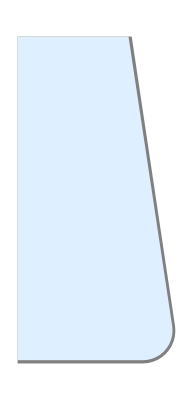

```mathematica
Ω=RoundedPolygon[{{0,0},{0,h},{tr,h},{br,0}},{0,0,0,bottomRounding}];
Β=RoundedPolygon[{{0,d},{0,h},{tr-d,h},{br-d,d}},{0,0,0,bottomRounding/(1+d)}];
Graphics[{{Gray,Ω},{LightBlue, Β}}]
```

```mathematica
maxCellMeasure=0.1;
```

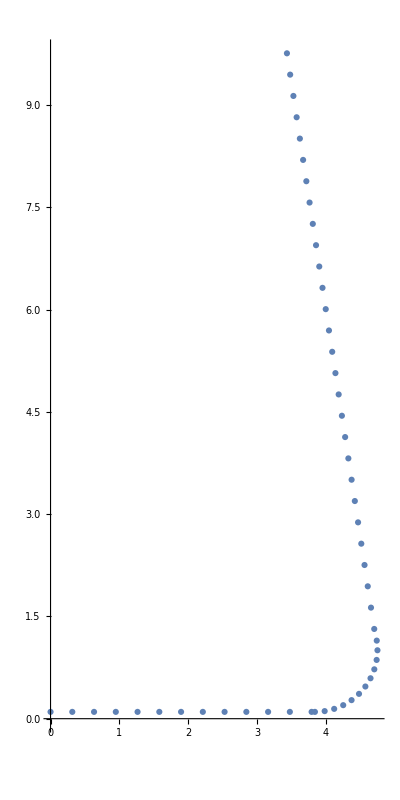
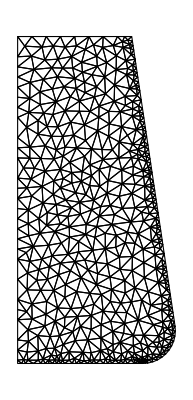

```mathematica
(* Add more points along medium contact line to make FEM elements smaller and improce accuracy *)
points={{0,d}}~Join~PolygonCoordinates[Β][[4;;]]~Join~{{tr-d,h}};
points=Flatten[MapThread[Table[#1 i+#2(1-i),{i,0,1,N[Sqrt[maxCellMeasure]/EuclideanDistance[#1,#2]]}]&,{points[[2;;]],points[[;;-2]]}],1];
mesh=ToElementMesh[Ω,{MaxCellMeasure->maxCellMeasure,"MeshOrder"->2,"IncludePoints"->points}];
{ListPlot[points, AspectRatio->2],mesh["Wireframe"]}
```

```mathematica
a[ρ_,γ_,τ_]:=Piecewise[{{1.0 4200 ,{ρ,γ}∈Β}},8.9 3450]/100;
k[ρ_,γ_,τ_]:=Piecewise[{{0.606,{ρ,γ}∈Β}},392]*100;
Bi:=0.0262*100;
sandTemperature=100;
```

```mathematica
u=NDSolveValue[{
D[(a[ρ,γ,τ]*T[ρ,γ,τ]), τ]==k[ρ,γ,τ]*(D[T[ρ,γ,τ], {ρ,2}]+D[T[ρ,γ,τ], {γ,2}])+
NeumannValue[0,ρ==0]+
NeumannValue[Bi T[ρ,γ,τ],(γ≥h hSand)&&(ρ>tr)]+
NeumannValue[Bi T[ρ,γ,τ],(γ==h)]
,
DirichletCondition[T[ρ,γ,τ]==sandTemperature,(ρ>0)&&(γ≤h hSand)],
T[ρ,γ,0]==0
},T,{τ,0,60}, {ρ,γ}∈mesh,Method->{
"PDEDiscretization"->{"MethodOfLines", "SpatialDiscretization"->"FiniteElement"}}];
```

```mathematica
densityPlotOfTurkishCovfefe[τ_,scaleColorFixedRange_:True]:=DensityPlot[
u[ρ,γ,τ],{ρ,γ}∈mesh,
PlotLegends->Automatic,
PlotRange->All,
FrameLabel->Automatic,
ColorFunction->If[scaleColorFixedRange, 
ColorData["M10DefaultDensityGradient"][Rescale[#,{0,110},{0,1}]]&,
ColorData["M10DefaultDensityGradient"]
],
ColorFunctionScaling->Not[scaleColorFixedRange],
PerformanceGoal->"Quality",
AspectRatio->h/Max[br,tr]];
```

```mathematica
Animate[densityPlotOfTurkishCovfefe[τ,False],{τ,0,30,0.1},
AnimationRunning->False, SaveDefinitions->False]
```